```mathematica
<<peeters`;
peeters`setGitDir["../project/figures/blogit"]
```

/Users/peeter/project/figures/blogit

```mathematica
<<MaTeX`

(*See MathematicaColorToLatexRGB.nb for color mapping logic.*)
SetOptions[MaTeX,"Preamble"->{"\\usepackage{xcolor,txfonts}","\\definecolor{BlueDarker}{HTML}{0000AA}","\\definecolor{RedDarker}{HTML}{AA0000}","\\definecolor{PurpleDarker}{HTML}{550055}","\\definecolor{OrangeDarker}{HTML}{AA5500}","\\definecolor{GreenDarker}{HTML}{00AA00}"},
"FontSize" -> 16]
```

MaTeX::shdw: Symbol MaTeX appears in multiple contexts {MaTeX`,Global`}; definitions in context MaTeX` may shadow or be shadowed by other definitions.

{BasePreamble→{\usepackage{lmodern,exscale},\usepackage{amsmath,amssymb}},Preamble→{\usepackage{xcolor,txfonts},\definecolor{BlueDarker}{HTML}{0000AA},\definecolor{RedDarker}{HTML}{AA0000},\definecolor{PurpleDarker}{HTML}{550055},\definecolor{OrangeDarker}{HTML}{AA5500},\definecolor{GreenDarker}{HTML}{00AA00}},DisplayStyle→True,ContentPadding→True,LineSpacing→{1.2,0},FontSize→16,Magnification→1,LogFileFunction→None,TeXFileFunction→None}

```mathematica
E^(I Pi) //Abs// N
Pi^(I E)  //Abs// N
I^(Pi E) //Abs// N

E^(I Pi) // N

Pi^(I E) // N
Cos[ E Log[Pi]] + I Sin[ E Log[Pi]]//N

I^(Pi E) // N
Cos[ E Pi^2/2 ] + I Sin[ E Pi^2/2 ]//N

 E Log[Pi] // N
E Pi^2/2 - 4 Pi// N
```

1.

1.

1.

-1.

-0.999553+0.0298898 ⅈ

-0.999553+0.0298898 ⅈ

0.661625+0.749835 ⅈ

0.661625+0.749835 ⅈ

3.1117

0.847813

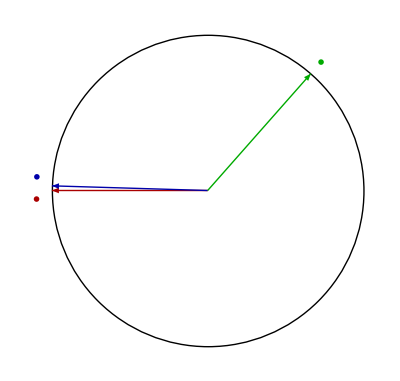

```mathematica
ClearAll[arrow, FunkyExponentsFig1, p]
p[theta_] := {Cos[ theta ], Sin[theta]};
arrow[ theta_ ] := Arrow[ {{0,0}, p[theta]} ];FunkyExponentsFig1 = Module[{t2,t3},
t2 = E Log[Pi];
t3 = E Pi^2/2;
Graphics[ {
Thick,
Circle[],
Arrowheads[0.1],
Red//Darker,
arrow[ Pi ],
Text[MaTeX["\\color{RedDarker}e^{i \\pi}"], 1.1 p[Pi + 0.05]],
Blue//Darker,
arrow[ t2 ],
Text[MaTeX["\\color{BlueDarker}\\pi^{e i}"], 1.1 p[t2 - 0.05]],
Green//Darker,
arrow[ t3 ],
Text[MaTeX["\\color{GreenDarker}i^{\\pi e}"], 1.1 p[t3]]
}]
]
```

```mathematica
peeters`exportForLatex["FunkyExponentsFig1",FunkyExponentsFig1]
```

{FunkyExponentsFig1.eps,FunkyExponentsFig1pn.png}

```mathematica
E^Pi // N
Pi^E // N
```

23.1407

22.4592